```mathematica
Remove["Global`*"]
```

```mathematica
PDF[PoissonDistribution[μ],k]
```

Piecewise[{{(ⅇ^-μ μ^k)/(k!), k≥0}, {0, True}}]

```mathematica
μ=10;Total[Table[{PDF[PoissonDistribution[μ],k]},{k,0,10}]]/10
```

{7281587/(5670 ⅇ^10)}

```mathematica
Mean[Table[PDF[PoissonDistribution[μ],k],{k,0,40}]]
```

20666464383469926621545899018271318761803503/(5709231208646623079794357257120554950852608 ⅇ^5)

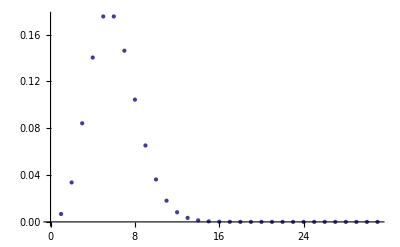

```mathematica
ListPlot[Table[PDF[PoissonDistribution[μ],k],{k,0,30}]]
```

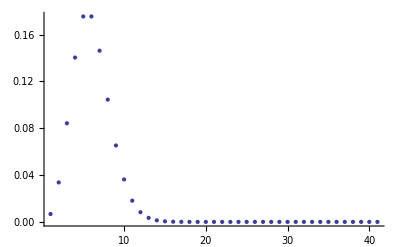

```mathematica
μ=5;
Show[ListPlot[Table[PDF[PoissonDistribution[μ],k],{k,0,40}]],PlotRange->All]
```

```mathematica
Mean[Table[PDF[PoissonDistribution[μ],k],{k,0,10}]]
```

9864101/(39916800 ⅇ)

```mathematica
N[Mean[Table[PDF[PoissonDistribution[μ],k],{k,0,10}]]]
```

0.0909091

```mathematica
Mean[PoissonDistribution[μ]]
```

1

```mathematica
Variance[PoissonDistribution[μ]]
```

1

```mathematica
Remove["Global`*"]
```

```mathematica
PDF[NormalDistribution[μ,σ],k]
```

(ⅇ^(-(k-μ)^2/(2 σ^2)))/(√(2 π) σ)

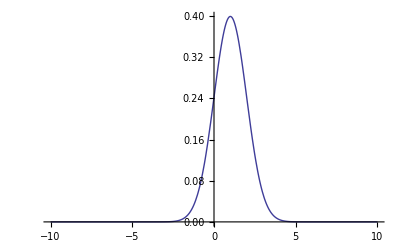

```mathematica
μ=1;σ=1;
Plot[PDF[NormalDistribution[μ,σ],x],{x,-10,10},PlotRange->All]
```

```mathematica
N[Total[Table[PDF[NormalDistribution[μ,σ],x],{x,-10,10}]]]
```

1.

```mathematica
Total[Table[PDF[NormalDistribution[μ,σ],x],{x,-10,10}]]
```

(√(2/π))/ⅇ^(81/2)+(√(2/π))/ⅇ^32+(√(2/π))/ⅇ^(49/2)+(√(2/π))/ⅇ^18+(√(2/π))/ⅇ^(25/2)+(√(2/π))/ⅇ^8+(√(2/π))/ⅇ^(9/2)+(√(2/π))/ⅇ^2+√(2/(ⅇ π))+1/(√(2 π))+1/(ⅇ^(121/2) √(2 π))+1/(ⅇ^50 √(2 π))

```mathematica
NIntegrate[x*PDF[NormalDistribution[μ,σ],x],{x,-10,10}]
```

1.

```mathematica
NIntegrate[x^2*PDF[NormalDistribution[μ,σ],x],{x,-10,10}]
```

2.

```mathematica
NIntegrate[x^3*PDF[NormalDistribution[μ,σ],x],{x,-10,10}]
```

4.

```mathematica
p=0.5;n=100;
Integrate[x*PDF[NormalDistribution[n,p],x],{x,-10,10}]
```

0.

```mathematica
Mean[BinomialDistribution[n,p]]
```

50.

```mathematica
N[Total[Table[PDF[BinomialDistribution[n,p],x],{x,0,n}]]]
```

1.

```mathematica
Integrate[x^2*PDF[NormalDistribution[n,p],x],{x,-10,10}]
```

0.

```mathematica
Integrate[x^3*PDF[NormalDistribution[n,p],x],{x,-10,10}]
```

0.

```mathematica
PDF[BinomialDistribution[n,p],x]
```

Piecewise[{{(1-p)^(n-x) p^x Binomial[n,x], 0≤x≤n}, {0, True}}]

```mathematica
(*
get random x
get random y
get x^2+y^2 and check if its ≤ 1
if yes, m+=1
*)
```

```mathematica
Table[m=0;For[i=0,i<Ns,i++,x=RandomReal[{0,1}];y=RandomReal[{0,1}];If[(x^2+y^2)<=1,m+=1]];Abs[N[(4*m/Ns-Pi)/Pi]],{Ns,100,1000,100}]
```

{0.108732,0.0376902,0.0111173,0.0227886,0.0578027,0.0101034,0.000402499,0.0148309,0.0185916,0.0297915}

```mathematica
Table[m=0;
For[j=0,j<10,j++,temp=0;
For[i=0,i<Ns,i++,x=RandomReal[{0,1}];y=RandomReal[{0,1}];If[(x^2+y^2)<=1,temp+=1]];
m+=temp];
N[4*m/10*Ns-Pi]
,{Ns,100,1000,100}]
```

{31876.9,125757.,284637.,496797.,779997.,1.11408×10^6,1.54336×10^6,2.01728×10^6,2.56032×10^6,3.152×10^6}

```mathematica
x=0;y=1;m=0
If[x^2+y^2≤1,m+=1]
```

0

1

```mathematica
(* wigner semi-circle*)
```

```mathematica
Remove["Global`*"]
```

```mathematica
M = MatrixForm[{{4,5,6},{1,2,3},{0,1,2}}]
```

(4 | 5 | 6
1 | 2 | 3
0 | 1 | 2)

```mathematica
Eigenvalues[M]
```

Eigenvalues[(4 | 5 | 6
1 | 2 | 3
0 | 1 | 2)]

```mathematica
M = For[i=0,i<3,i++,Print[
RandomReal[{0,1}]]]
```

0.394364

0.165947

0.230677

```mathematica
M
```

```mathematica
M = {}
```

{}

```mathematica
row = {}
```

{}

```mathematica
AppendTo[row,{1,2,3}]
```

{{1,2,3}}

```mathematica
AppendTo[M,{1,2,3}]
```

{{1,2,3}}

```mathematica
AppendTo[M,{1,2,3}]
```

{{1,2,3},{1,2,3}}

```mathematica
M={}
For[j=0,j<3,j++,
row ={};
For[i=0,i<3,i++,AppendTo[row,RandomReal[{0,1}]]];
AppendTo[M,row]]
```

{}

```mathematica
M
```

{{0.727746,0.441952,0.740821},{0.822447,0.738628,0.550036},{0.283263,0.757536,0.615495}}

```mathematica
Eigenvalues[M]
```

{1.89424,0.0938151+0.293019 ⅈ,0.0938151-0.293019 ⅈ}

```mathematica
AppendTo[row,RandomReal[{0,1}]]
```

{0.791085,0.748534,0.265794}

```mathematica
M = IdentityMatrix[3]
```

```mathematica
M =ConstantArray[0,{3,3}]
For[i=0,i<3,i++,For[j=i,j<3,j++,M[i,j]=RandomReal[{0,1}]]]
```

{{0,0,0},{0,0,0},{0,0,0}}

Set::write: Tag List in {{0, 0, 0}, {0, 0, 0}, {0, 0, 0}}[0, 0] is Protected.

Set::write: Tag List in {{0, 0, 0}, {0, 0, 0}, {0, 0, 0}}[0, 1] is Protected.

Set::write: Tag List in {{0, 0, 0}, {0, 0, 0}, {0, 0, 0}}[0, 2] is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

```mathematica
M =ConstantArray[0,{3,3}]
Table[RandomReal[{0,1}],{i,3},{j,3}]
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0.0362478,0.91452,0.152184},{0.582028,0.10816,0.84855},{0.221465,0.197766,0.448914}}

```mathematica
M = Table[If[i≤j,RandomReal[{0,1}]],{i,3},{j,3}]
```

{{0.492294,0.123914,0.102856},{Null,0.0259605,0.939245},{Null,Null,0.916952}}

```mathematica
M = Table[Which[i≤j,RandomReal[{0,1}],i>j,0],{i,3},{j,3}]
```

{{0.893305,0.988085,0.272098},{0,0.675789,0.904382},{0,0,0.212539}}

```mathematica
temp = Table[Which[i≤j,RandomReal[{0,1}],i>j,0],{i,3},{j,3}]
```

{{0.140421,0.580133,0.908437},{0,0.757397,0.220939},{0,0,0.803185}}

```mathematica
Table[Which[i≤j,temp[i,j],i>j,temp[j,i]],{i,3},{j,3}]
```

```mathematica
temp[1,1]
```

{{0.140421,0.580133,0.908437},{0,0.757397,0.220939},{0,0,0.803185}}[1,1]

```mathematica
Table[N[temp[i,j]],{i,3},{j,3}]
```

{{{{0.140421,0.580133,0.908437},{0.,0.757397,0.220939},{0.,0.,0.803185}}[1.,1.],{{0.140421,0.580133,0.908437},{0.,0.757397,0.220939},{0.,0.,0.803185}}[1.,2.],{{0.140421,0.580133,0.908437},{0.,0.757397,0.220939},{0.,0.,0.803185}}[1.,3.]},{{{0.140421,0.580133,0.908437},{0.,0.757397,0.220939},{0.,0.,0.803185}}[2.,1.],{{0.140421,0.580133,0.908437},{0.,0.757397,0.220939},{0.,0.,0.803185}}[2.,2.],{{0.140421,0.580133,0.908437},{0.,0.757397,0.220939},{0.,0.,0.803185}}[2.,3.]},{{{0.140421,0.580133,0.908437},{0.,0.757397,0.220939},{0.,0.,0.803185}}[3.,1.],{{0.140421,0.580133,0.908437},{0.,0.757397,0.220939},{0.,0.,0.803185}}[3.,2.],{{0.140421,0.580133,0.908437},{0.,0.757397,0.220939},{0.,0.,0.803185}}[3.,3.]}}

```mathematica
M
```

{{0.492294,0.123914,0.102856},{Null,0.0259605,0.939245},{Null,Null,0.916952}}

```mathematica
For[i=0,i<3,i++,
For[j=0,j<3,j++,
If[i>j,M[j,i]=M[i,j]]
]
]
```

Set::write: Tag List in {{0.893305, 0.988085, 0.272098}, {0, 0.675789, 0.904382}, {0, 0, 0.212539}}[0, 1] is Protected.

Set::write: Tag List in {{0.893305, 0.988085, 0.272098}, {0, 0.675789, 0.904382}, {0, 0, 0.212539}}[0, 2] is Protected.

Set::write: Tag List in {{0.893305, 0.988085, 0.272098}, {0, 0.675789, 0.904382}, {0, 0, 0.212539}}[1, 2] is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

```mathematica
M
```

{{0.893305,0.988085,0.272098},{0,0.675789,0.904382},{0,0,0.212539}}

```mathematica
(M = {{1,2},{3,4}})
```

{{1,2},{3,4}}

```mathematica
M[1,1]=1
```

Set::write: Tag List in {{1, 2}, {3, 4}}[1, 1] is Protected.

1

```mathematica
M[1,1]//MatrixForm
```

{{1,2},{3,4}}[1,1]

```mathematica
a = RandomReal[{0,1},{3,3}]//MatrixForm
```

(0.448335 | 0.875608 | 0.970085
0.384535 | 0.91569 | 0.0686945
0.199655 | 0.545272 | 0.0277274)

```mathematica
Table[a[i,j],{i,3},{j,3}]
```

{{(0.448335 | 0.875608 | 0.970085
0.384535 | 0.91569 | 0.0686945
0.199655 | 0.545272 | 0.0277274)[1,1],(0.448335 | 0.875608 | 0.970085
0.384535 | 0.91569 | 0.0686945
0.199655 | 0.545272 | 0.0277274)[1,2],(0.448335 | 0.875608 | 0.970085
0.384535 | 0.91569 | 0.0686945
0.199655 | 0.545272 | 0.0277274)[1,3]},{(0.448335 | 0.875608 | 0.970085
0.384535 | 0.91569 | 0.0686945
0.199655 | 0.545272 | 0.0277274)[2,1],(0.448335 | 0.875608 | 0.970085
0.384535 | 0.91569 | 0.0686945
0.199655 | 0.545272 | 0.0277274)[2,2],(0.448335 | 0.875608 | 0.970085
0.384535 | 0.91569 | 0.0686945
0.199655 | 0.545272 | 0.0277274)[2,3]},{(0.448335 | 0.875608 | 0.970085
0.384535 | 0.91569 | 0.0686945
0.199655 | 0.545272 | 0.0277274)[3,1],(0.448335 | 0.875608 | 0.970085
0.384535 | 0.91569 | 0.0686945
0.199655 | 0.545272 | 0.0277274)[3,2],(0.448335 | 0.875608 | 0.970085
0.384535 | 0.91569 | 0.0686945
0.199655 | 0.545272 | 0.0277274)[3,3]}}

```mathematica
a[]
```

{{0.769317,0.220483,0.582079},{0.677902,0.891632,0.482256},{0.191873,0.621109,0.377544}}[]

```mathematica
b = {{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
b[1]
```

{{1,2},{3,4}}[1]